# Integrations from Γ_0 (reactant minimum) for shifted Fermi distribution and various models of density of states (DOS)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/CABES/UPD-Hydrogen-Pt-D2O/mathematica

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
```

## Units and constants

### Unit conversion factors

```mathematica
bohr2a=QuantityMagnitude@UnitConvert[Quantity[1,"BohrRadius"],"Angstroms"];
a2bohr=1/bohr2a;
au2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2au=1/au2kcal;
ev2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2ev=1/ev2kcal;
ev2cm=QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2ev=1/ev2cm;
au2ev=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"];
ev2au=1/au2ev;
au2cm=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2au=1/au2cm;
a2m=10^-10;
m2a=1/a2m;
m2bohr=m2a a2bohr;
bohr2m=1/m2bohr;
debye2SI=QuantityMagnitude@UnitConvert[Quantity[1,"Debyes"],"Coulomb"*"Meters"];
debye2au=QuantityMagnitude@UnitConvert[Quantity[1,"Debyes"],"ElementaryCharge"*"BohrRadius"];
au2ps=QuantityMagnitude@UnitConvert[1/(2π)Entity["PhysicalConstant","PlanckConstant"]["Value"],"Hartrees*ps"];
ps2au=1/au2ps;
au2s=au2ps*10^-12;
s2au=1/au2s;
```

### Universal constants

```mathematica
ℏ=1; (* in atomic units *)
hbar=QuantityMagnitude@Entity["PhysicalConstant","ReducedPlanckConstant"]["Value"]; (* in Joule × seconds *)
hbaraups=1 au2ps; (* in Hartree × ps *)
hbarkcalps=hbaraups au2kcal; (* in kcal/mol × ps *)
Dalton=QuantityMagnitude@UnitConvert[1 Quantity[, "Daltons"],"electronmass"];
μH=QuantityMagnitude@UnitConvert[Quantity[, "ProtonMass"],"electronmass"];
μD=QuantityMagnitude@UnitConvert[Quantity[, "DeuteronMass"],"electronmass"];
MassH=μH/Dalton;
MassD=μD/Dalton;
kb=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"];
kB=QuantityMagnitude@Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
NAvogadro=QuantityMagnitude@Entity["PhysicalConstant","AvogadroConstant"]["Value"];
R=kB×NAvogadro;
elcharge=QuantityMagnitude@Entity["PhysicalConstant","ElementaryCharge"]["Value"];
elchargeμC=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","ElementaryCharge"]["Value"],"microCoulombs"];
F=QuantityMagnitude@Entity["PhysicalConstant","FaradayConstant"]["Value"];
ε0=QuantityMagnitude@Entity["PhysicalConstant","ElectricConstant"]["Value"];
hbar=QuantityMagnitude@Entity["PhysicalConstant","ReducedPlanckConstant"]["Value"];
Debye=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"];
```

## Rectangular density of states

```mathematica
ρθ[x_,A_,B_]:=1/(B-A)HeavisideTheta[x-A]HeavisideTheta[B-x];
ρU[x_,A_,B_]:=1/(B-A)UnitStep[x-A]UnitStep[B-x];
```

Can also be represented by the probability density function (PDF) for a uniform distribution:

```mathematica
ρPDF[x_,A_,B_]:=PDF[UniformDistribution[{A,B}],x];
```

```mathematica
Manipulate[
Plot[ρPDF[x,A,B],{x,-10,10}],
{A,-9,-1},
{B,1,9}
]
```

### With Fermi distribution:

```mathematica
Intθ=Integrate[ρθ[x+δ,A,B]/(1+Exp[(x+δ)/kT]),{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
IntU=Integrate[ρU[x+δ,A,B]/(1+Exp[(x+δ)/kT]),{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

```mathematica
Intθs=FullSimplify[Intθ,Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
IntUs=FullSimplify[IntU,Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

```mathematica
Integrate[ρPDF[x+δ,A,B]/(1+Exp[(x+δ)/kT]),{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

(Piecewise[{{-(-B+Γ+δ+kT Log[1+ⅇ^(B/kT)]-kT Log[1+ⅇ^((Γ+δ)/kT)])/(A-B), (B>A&&A≤Γ<B&&0<δ<B-Γ&&ϵ>B-δ)||(B>A&&Γ<A&&A-Γ<δ<B-Γ&&ϵ>B-δ)}, {(-Γ+ϵ+kT Log[1+ⅇ^((Γ+δ)/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), (B>A&&A≤Γ<B&&0<δ<B-Γ&&Γ<ϵ≤B-δ)||(B>A&&Γ<A&&A-Γ<δ<B-Γ&&Γ<ϵ≤B-δ)}, {-1+(kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(B/kT))])/(A-B), (B>A&&Γ<A&&δ==A-Γ&&ϵ>B-δ)||(B>A&&Γ<A&&0<δ<A-Γ&&ϵ>B-δ)}, {(-A+δ+ϵ+kT Log[1+ⅇ^(A/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), (B>A&&Γ<A&&δ==A-Γ&&A-δ<ϵ≤B-δ)||(B>A&&Γ<A&&0<δ<A-Γ&&A-δ<ϵ≤B-δ)}, {0, True}}])+(Piecewise[{{(-Γ+ϵ+kT Log[1+ⅇ^((Γ+δ)/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), (B>A&&A≤Γ<B&&0<δ<B-Γ&&A-δ≤ϵ<Γ)||(B>A&&Γ<A&&A-Γ<δ<B-Γ&&A-δ<ϵ<Γ)}, {-(-A+Γ+δ+kT Log[1+ⅇ^(A/kT)]-kT Log[1+ⅇ^((Γ+δ)/kT)])/(A-B), (B>A&&A≤Γ<B&&0<δ<B-Γ&&ϵ<A-δ)||(B>A&&Γ<A&&A-Γ<δ<B-Γ&&ϵ==A-δ)||(B>A&&Γ<A&&A-Γ<δ<B-Γ&&ϵ<A-δ)}, {(-B+δ+ϵ+kT Log[1+ⅇ^(B/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), (B>A&&Γ≥B&&δ>0&&A-δ≤ϵ<B-δ)||(B>A&&A≤Γ<B&&δ==B-Γ&&A-δ≤ϵ<B-δ)||(B>A&&A≤Γ<B&&δ>B-Γ&&A-δ≤ϵ<B-δ)||(B>A&&Γ<A&&δ==B-Γ&&A-δ≤ϵ<B-δ)||(B>A&&Γ<A&&δ>B-Γ&&A-δ≤ϵ<B-δ)}, {1+(kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^(A/kT))])/(A-B), (B>A&&Γ≥B&&δ>0&&ϵ<A-δ)||(B>A&&A≤Γ<B&&δ==B-Γ&&ϵ<A-δ)||(B>A&&A≤Γ<B&&δ>B-Γ&&ϵ<A-δ)||(B>A&&Γ<A&&δ==B-Γ&&ϵ<A-δ)||(B>A&&Γ<A&&δ>B-Γ&&ϵ<A-δ)}, {0, True}}])

```mathematica
FullSimplify[%]
```

(Piecewise[{{-(-B+Γ+δ+kT Log[1+ⅇ^(B/kT)]-kT Log[1+ⅇ^((Γ+δ)/kT)])/(A-B), B>A&&δ+ϵ>B&&((δ>0&&Γ+δ<B&&A≤Γ)||(A<Γ+δ&&B>Γ+δ&&Γ<A))}, {(-Γ+ϵ+kT Log[1+ⅇ^((Γ+δ)/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), B>A&&Γ<ϵ&&B≥δ+ϵ&&((δ>0&&A≤Γ)||(A<Γ+δ&&Γ<A))}, {-1+(kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(B/kT))])/(A-B), (A==Γ+δ||(δ>0&&A>Γ+δ))&&Γ<A&&B>A&&δ+ϵ>B}, {(-A+δ+ϵ+kT Log[1+ⅇ^(A/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), (A==Γ+δ||(δ>0&&A>Γ+δ))&&A<δ+ϵ&&B≥δ+ϵ&&Γ<A}, {0, True}}])+(Piecewise[{{(-Γ+ϵ+kT Log[1+ⅇ^((Γ+δ)/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), B>A&&((δ>0&&Γ+δ<B&&A≤Γ&&A≤δ+ϵ&&ϵ<Γ)||(B>Γ+δ&&A<δ+ϵ&&Γ>ϵ&&Γ<A))}, {-(-A+Γ+δ+kT Log[1+ⅇ^(A/kT)]-kT Log[1+ⅇ^((Γ+δ)/kT)])/(A-B), B>A&&((A<Γ+δ&&B>Γ+δ&&Γ<A&&A≥δ+ϵ)||(δ>0&&Γ+δ<B&&A≤Γ&&δ+ϵ<A))}, {(-B+δ+ϵ+kT Log[1+ⅇ^(B/kT)]-kT Log[1+ⅇ^((δ+ϵ)/kT)])/(A-B), A≤δ+ϵ&&B>δ+ϵ&&(((A>Γ||B>Γ)&&B≤Γ+δ)||(Γ≥B&&δ>0))}, {1+(kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^(A/kT))])/(A-B), B>A&&δ+ϵ<A&&(((A>Γ||B>Γ)&&B≤Γ+δ)||(Γ≥B&&δ>0))}, {0, True}}])

```mathematica
BypassIntFermi[ϵ_,Γ_,δ_,A_,B_,T_]:=Module[{kT},
kT=kb T au2kcal;
1/(B-A)Piecewise[{{A+kT Log[(1+ⅇ^(-B/kT))/(1+ⅇ^(A/kT))], B<δ+ϵ&&A>Γ+δ}, {-A+B+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(B/kT))], B<Γ+δ&&A>δ+ϵ}, {-A+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(-(Γ+δ)/kT))], A<Γ+δ&&B≥Γ+δ&&A>δ+ϵ}, {2 kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^((Γ+δ)/kT))], A==Γ+δ&&A>δ+ϵ}, {-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))], B≥Γ+δ&&B<δ+ϵ&&A≤Γ+δ}, {B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))], B<Γ+δ&&B≥δ+ϵ&&A≤δ+ϵ}, {A-δ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^(A/kT))], A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ}, {Γ+δ+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^((Γ+δ)/kT))], B≥Γ+δ&&Γ>ϵ&&A≤δ+ϵ}, {kT Log[((1+ⅇ^((δ+ϵ)/kT))^2)/((1+ⅇ^(A/kT))^2)], A==δ+ϵ&&A>Γ+δ}, {Γ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^((Γ+δ)/kT))], Γ<ϵ&&B≥δ+ϵ&&A≤Γ+δ}, {0, True}}]
];
```

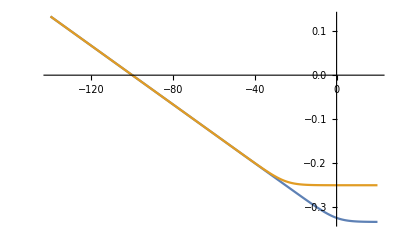

```mathematica
Plot[{
BypassIntFermi[x,-100,0,-150,150,2000],
BypassIntFermi[x,-100,25,-150,150,2000]},
{x,-140,20}]
```

### With UnitStep distribution:

```mathematica
IntUstep=Integrate[ρU[x+δ,A,B]UnitStep[-x-δ],{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,δ>0,A<B,ϵ<B}]
```

1/(-A+B)(UnitStep[-A+Γ+δ] UnitStep[Γ-ϵ] (-((UnitStep[-Γ-δ] UnitStep[A-Γ-δ] (-((-1+UnitStep[-A]) ((-B+Γ+δ+B UnitStep[B]) UnitStep[-Γ-δ] UnitStep[B-Γ-δ]+UnitStep[B] (B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ+δ]))+UnitStep[-A] ((-A+Γ+δ) UnitStep[A-Γ-δ] UnitStep[B-Γ-δ]+(-A+B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[-A+Γ+δ]))+UnitStep[-A] UnitStep[-A+Γ+δ] ((A UnitStep[A] UnitStep[B]+UnitStep[-A] (A-B+B UnitStep[B])) (-1+UnitStep[-Γ-δ])+UnitStep[-Γ-δ] ((-A+Γ+δ) UnitStep[A-Γ-δ] UnitStep[B-Γ-δ]+(-A+B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[-A+Γ+δ]))) (-1+UnitStep[-A+δ+ϵ]))+(UnitStep[-Γ-δ] UnitStep[-Γ+ϵ] (-(((-B+Γ+δ+B UnitStep[B]) UnitStep[-Γ-δ] UnitStep[B-Γ-δ]+UnitStep[B] (B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ+δ]) (-1+UnitStep[-δ-ϵ]))+UnitStep[-δ-ϵ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ]))+UnitStep[Γ-ϵ] UnitStep[-δ-ϵ] (UnitStep[-Γ-δ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ])-(-1+UnitStep[-Γ-δ]) (-((-B+δ+ϵ+B UnitStep[B]) UnitStep[-δ-ϵ] UnitStep[B-δ-ϵ])+UnitStep[B] (-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[δ+ϵ]))) UnitStep[-A+δ+ϵ])+UnitStep[-Γ+ϵ] UnitStep[-A+δ+ϵ] (UnitStep[-A+Γ+δ] (UnitStep[-Γ-δ] UnitStep[-Γ+ϵ] (-(((-B+Γ+δ+B UnitStep[B]) UnitStep[-Γ-δ] UnitStep[B-Γ-δ]+UnitStep[B] (B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ+δ]) (-1+UnitStep[-δ-ϵ]))+UnitStep[-δ-ϵ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ]))+UnitStep[Γ-ϵ] UnitStep[-δ-ϵ] (UnitStep[-Γ-δ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ])-(-1+UnitStep[-Γ-δ]) (-((-B+δ+ϵ+B UnitStep[B]) UnitStep[-δ-ϵ] UnitStep[B-δ-ϵ])+UnitStep[B] (-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[δ+ϵ])))-(-1+UnitStep[-A+Γ+δ]) (UnitStep[-δ-ϵ] UnitStep[A-δ-ϵ] (-((-1+UnitStep[-A]) (-((-B+δ+ϵ+B UnitStep[B]) UnitStep[-δ-ϵ] UnitStep[B-δ-ϵ])+UnitStep[B] (-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[δ+ϵ]))+UnitStep[-A] ((A-δ-ϵ) UnitStep[A-δ-ϵ] UnitStep[B-δ-ϵ]+(A-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-A+δ+ϵ]))+UnitStep[-A] UnitStep[-A+δ+ϵ] (-((A UnitStep[A] UnitStep[B]+UnitStep[-A] (A-B+B UnitStep[B])) (-1+UnitStep[-δ-ϵ]))+UnitStep[-δ-ϵ] ((A-δ-ϵ) UnitStep[A-δ-ϵ] UnitStep[B-δ-ϵ]+(A-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-A+δ+ϵ])))))

```mathematica
IntUsteps=FullSimplify[IntUstep,Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

Piecewise[{{-1, (B<0||δ+ϵ≤0)&&(B<δ+ϵ||δ+ϵ>0)&&A≤0&&A>Γ+δ&&Γ≤ϵ}, {1, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&Γ≥ϵ&&A≤0&&A>δ+ϵ}, {0, (δ+ϵ≤0&&((Γ==ϵ&&B≥δ+ϵ&&A≤δ+ϵ)||(A≥δ+ϵ&&A>Γ+δ)||(B<Γ+δ&&((B<δ+ϵ&&Γ+δ≤0)||Γ<ϵ))))||(A≥0&&((A>Γ+δ&&δ+ϵ>0)||(A>δ+ϵ&&Γ+δ>0)))||(A>δ+ϵ&&((A>0&&A<Γ+δ)||(A≥Γ+δ&&Γ+δ≤0)||Γ<ϵ||A>Γ+δ))||(B<0&&((B<Γ+δ&&(B<δ+ϵ||δ+ϵ>0))||(Γ+δ>0&&B<δ+ϵ)))||(B<Γ+δ&&Γ+δ<0&&(B<δ+ϵ||δ+ϵ>0))||(Γ<ϵ&&A≤Γ+δ&&((B≥Γ+δ&&Γ+δ≥0)||Γ+δ>0))||(B<δ+ϵ&&(δ+ϵ<0||Γ+δ≤0)&&(Γ>ϵ||Γ+δ>0))||(A≤δ+ϵ&&((Γ>ϵ&&((B≥δ+ϵ&&δ+ϵ≥0)||δ+ϵ>0))||(A≤Γ+δ&&Γ+δ>0&&δ+ϵ>0)))||(A>Γ+δ&&(A>0||Γ>ϵ))}, {A/(-A+B), A<0&&B≥0&&A>Γ+δ&&δ+ϵ>0}, {A/(A-B), A<0&&B≥0&&Γ+δ>0&&A>δ+ϵ}, {-(Γ+δ)/(A-B), B≥0&&Γ+δ<0&&δ+ϵ>0&&A≤Γ+δ}, {-(-A+Γ+δ)/(A-B), A<Γ+δ&&B≥Γ+δ&&Γ+δ≤0&&A>δ+ϵ}, {-(-B+Γ+δ)/(A-B), (B<0||δ+ϵ≤0)&&B≥Γ+δ&&Γ<ϵ&&(B<δ+ϵ||δ+ϵ>0)&&A≤Γ+δ&&Γ+δ≤0}, {(-Γ+ϵ)/(A-B), B≥Γ+δ&&Γ≠ϵ&&B≥δ+ϵ&&A≤Γ+δ&&Γ+δ≤0&&A≤δ+ϵ&&δ+ϵ≤0}, {(δ+ϵ)/(A-B), B≥0&&δ+ϵ<0&&Γ+δ>0&&A≤δ+ϵ}, {(-A+δ+ϵ)/(A-B), A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ&&δ+ϵ≤0}, {(-B+δ+ϵ)/(A-B), True}}]

```mathematica
TraditionalForm[IntUsteps]
```

Piecewise[{{-1, (B<0∨δ+ϵ≤0)∧(B<δ+ϵ∨δ+ϵ>0)∧A≤0∧A>Γ+δ∧Γ≤ϵ}, {1, (B<0∨Γ+δ≤0)∧(B<Γ+δ∨Γ+δ>0)∧Γ≥ϵ∧A≤0∧A>δ+ϵ}, {0, (δ+ϵ≤0∧((Γ==ϵ∧B≥δ+ϵ∧A≤δ+ϵ)∨(A≥δ+ϵ∧A>Γ+δ)∨(B<Γ+δ∧((B<δ+ϵ∧Γ+δ≤0)∨Γ<ϵ))))∨(A≥0∧((A>Γ+δ∧δ+ϵ>0)∨(A>δ+ϵ∧Γ+δ>0)))∨(A>δ+ϵ∧((A>0∧A<Γ+δ)∨(A≥Γ+δ∧Γ+δ≤0)∨Γ<ϵ∨A>Γ+δ))∨(B<0∧((B<Γ+δ∧(B<δ+ϵ∨δ+ϵ>0))∨(Γ+δ>0∧B<δ+ϵ)))∨(B<Γ+δ∧Γ+δ<0∧(B<δ+ϵ∨δ+ϵ>0))∨(Γ<ϵ∧A≤Γ+δ∧((B≥Γ+δ∧Γ+δ≥0)∨Γ+δ>0))∨(B<δ+ϵ∧(δ+ϵ<0∨Γ+δ≤0)∧(Γ>ϵ∨Γ+δ>0))∨(A≤δ+ϵ∧((Γ>ϵ∧((B≥δ+ϵ∧δ+ϵ≥0)∨δ+ϵ>0))∨(A≤Γ+δ∧Γ+δ>0∧δ+ϵ>0)))∨(A>Γ+δ∧(A>0∨Γ>ϵ))}, {A/(B-A), A<0∧B≥0∧A>Γ+δ∧δ+ϵ>0}, {A/(A-B), A<0∧B≥0∧Γ+δ>0∧A>δ+ϵ}, {-(Γ+δ)/(A-B), B≥0∧Γ+δ<0∧δ+ϵ>0∧A≤Γ+δ}, {-(-A+Γ+δ)/(A-B), A<Γ+δ∧B≥Γ+δ∧Γ+δ≤0∧A>δ+ϵ}, {-(-B+Γ+δ)/(A-B), (B<0∨δ+ϵ≤0)∧B≥Γ+δ∧Γ<ϵ∧(B<δ+ϵ∨δ+ϵ>0)∧A≤Γ+δ∧Γ+δ≤0}, {(ϵ-Γ)/(A-B), B≥Γ+δ∧Γ≠ϵ∧B≥δ+ϵ∧A≤Γ+δ∧Γ+δ≤0∧A≤δ+ϵ∧δ+ϵ≤0}, {(δ+ϵ)/(A-B), B≥0∧δ+ϵ<0∧Γ+δ>0∧A≤δ+ϵ}, {(-A+δ+ϵ)/(A-B), A<δ+ϵ∧B≥δ+ϵ∧A>Γ+δ∧δ+ϵ≤0}, {(-B+δ+ϵ)/(A-B), True}}]

```mathematica
BypassIntStep[ϵ_,Γ_,δ_,A_,B_,T_]:=Module[{kT},
1/(B-A)Piecewise[{{0, (δ+ϵ≤0&&((Γ==ϵ&&B≥δ+ϵ&&A≤δ+ϵ)||(A≥δ+ϵ&&A>Γ+δ)||(B<Γ+δ&&((B<δ+ϵ&&Γ+δ≤0)||Γ<ϵ))))||(A≥0&&((A>Γ+δ&&δ+ϵ>0)||(A>δ+ϵ&&Γ+δ>0)))||(A>δ+ϵ&&((A>0&&A<Γ+δ)||(A≥Γ+δ&&Γ+δ≤0)||Γ<ϵ||A>Γ+δ))||(B<0&&((δ+ϵ>0&&B<Γ+δ)||(Γ+δ>0&&B<δ+ϵ)))||(B<Γ+δ&&Γ+δ<0&&(B<δ+ϵ||δ+ϵ>0))||(Γ<ϵ&&A≤Γ+δ&&((B≥Γ+δ&&Γ+δ≥0)||Γ+δ>0))||(B<δ+ϵ&&(δ+ϵ<0||Γ+δ≤0)&&(Γ>ϵ||Γ+δ>0))||(A>Γ+δ&&(A>0||Γ>ϵ))||(δ+ϵ>0&&A≤δ+ϵ&&((Γ+δ>0&&A≤Γ+δ)||Γ>ϵ))}, {-A, A<0&&B≥0&&Γ+δ>0&&A>δ+ϵ}, {A, A<0&&B≥0&&A>Γ+δ&&δ+ϵ>0}, {A-B, (B<0||δ+ϵ≤0)&&(B<δ+ϵ||δ+ϵ>0)&&A≤0&&A>Γ+δ&&Γ≤ϵ}, {-A+B, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&Γ≥ϵ&&A≤0&&A>δ+ϵ}, {Γ+δ, B≥0&&Γ+δ<0&&δ+ϵ>0&&A≤Γ+δ}, {-A+Γ+δ, A<Γ+δ&&B≥Γ+δ&&Γ+δ≤0&&A>δ+ϵ}, {-B+Γ+δ, (B<0||δ+ϵ≤0)&&B≥Γ+δ&&Γ<ϵ&&(B<δ+ϵ||δ+ϵ>0)&&A≤Γ+δ&&Γ+δ≤0}, {Γ-ϵ, B≥Γ+δ&&Γ≠ϵ&&B≥δ+ϵ&&A≤Γ+δ&&Γ+δ≤0&&A≤δ+ϵ&&δ+ϵ≤0}, {-δ-ϵ, B≥0&&δ+ϵ<0&&Γ+δ>0&&A≤δ+ϵ}, {A-δ-ϵ, A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ&&δ+ϵ≤0}, {B-δ-ϵ, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&B≥δ+ϵ&&Γ>ϵ&&A≤δ+ϵ&&δ+ϵ≤0}, {-2 (δ+ϵ), True}}]];
```

```mathematica
BypassIntStepW[ϵ_,Γ_,δ_,A_,B_,T_]:=Module[{Γδ,ϵδ,B1,B2},
Γδ=Γ+δ;
ϵδ=ϵ+δ;
B1=Piecewise[{
{CDF[UniformDistribution[{A,B}],0],Γδ>0},
{CDF[UniformDistribution[{A,B}],Γδ],Γδ≤0}
}];
B2=Piecewise[{
{CDF[UniformDistribution[{A,B}],0],ϵδ>0},
{CDF[UniformDistribution[{A,B}],ϵδ],ϵδ≤0}
}];
B1-B2
];
```

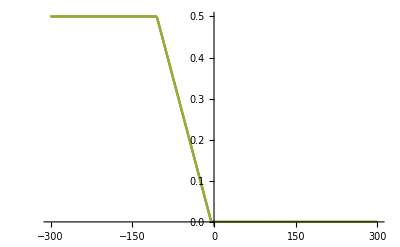

```mathematica
Plot[{BypassIntStep[x,2,5,-100,100,300],BypassIntStepW[x,2,5,-100,100,300],BypassIntFermi[x,2,5,-100,100,300]},{x,-300,300},PlotRange->All]
```

## Semieliptical density of states (Wigner Semicircle distribution)

```mathematica
ρSE[x_,ϵc_,γ_]:=Piecewise[{
{2/(π γ)√(1-((x-ϵc)/γ)^2),-γ<x-ϵc<γ}
}];
```

```mathematica
Manipulate[
Plot[ρSE[x,ϵc,γ],{x,-2,2},
PlotRange->{-0.1,1},
Axes->False,Frame->True,
FrameLabel->{"ϵ-ϵ_F","DOS"},
GridLines->{None,{0}}],
{{ϵc,0,"ϵ_c"},-2,2},
{{γ,1},0.5,2},
FrameLabel->{None,None,"Semieliptical Band: 2/(π  γ)√(1 - SuperscriptBox[(FractionBox[ϵ - SubscriptBox[ϵ, c], γ]), 2])"}
]
```

### Now the integral with the Fermi distribution function

```mathematica
NIntSEFermi[ϵ_,Γ_,δ_,ϵc_,γ_,T_]:=NIntegrate[ρSE[y,ϵc,γ]/(1+Exp[y/(kb T au2kcal)]),{y,ϵ+δ,Γ+δ},MinRecursion->10,MaxRecursion->20,WorkingPrecision->10];
```

```mathematica
Plot[{NIntSEFermi[ϵ,-2,1,0,2,300]},{ϵ,-5,5},PlotStyle->{Black,{Black,Dashed}}]
```

$Aborted

### Now the integral with the UnitStep function

```mathematica
IntSEStepW[ϵ_,Γ_,δ_,ϵc_,γ_]:=Module[{Γδ,ϵδ,B1,B2},
Γδ=Γ+δ;
ϵδ=ϵ+δ;
B1=Piecewise[{
{CDF[WignerSemicircleDistribution[ϵc,γ],0],Γδ>0},
{CDF[WignerSemicircleDistribution[ϵc,γ],Γδ],Γδ≤0}
}];
B2=Piecewise[{
{CDF[WignerSemicircleDistribution[ϵc,γ],0],ϵδ>0},
{CDF[WignerSemicircleDistribution[ϵc,γ],ϵδ],ϵδ≤0}
}];
B1-B2
];
```

```mathematica
NIntSEStep[ϵ_,Γ_,δ_,ϵc_,γ_]:=NIntegrate[ρSE[y,ϵc,γ]UnitStep[-y],{y,ϵ+δ,Γ+δ},MinRecursion->7];
```

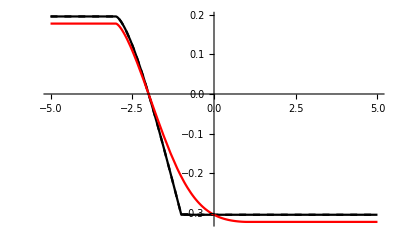

```mathematica
Plot[{NIntSEStep[ϵ,-2,1,0,2],IntSEStepW[ϵ,-2,1,0,2],NIntSEFermi[ϵ,-2,1,0,2,300]},{ϵ,-5,5},PlotStyle->{Black,{Black,Dashed},Red}]
```

## Triangular density of states

```mathematica
ρTR[x_,ϵc_,{ϵmin_,ϵmax_}]:=Piecewise[{
{(2(-ϵmin+x))/((ϵc-ϵmin)(ϵmax-ϵmin)),ϵmin<x<ϵc},
{(2(ϵmax-x))/((-ϵc+ϵmax)(ϵmax-ϵmin)),ϵc<x<ϵmax}
},0];
```

```mathematica
Integrate[ρTR[x,ϵc,{ϵmin,ϵmax}],{x,ϵmin,ϵmax},Assumptions->{ϵc∈Reals,ϵmin∈Reals,ϵmax∈Reals,ϵmax>ϵmin,ϵmin<ϵc<ϵmax}]
```

1

```mathematica
Manipulate[
Plot[ρTR[x,ϵc,{ϵmin,ϵmax}],{x,-5,5},
PlotRange->{-0.1,0.5},
Axes->False,Frame->True,
FrameLabel->{"ϵ-ϵ_F","DOS"},
GridLines->{None,{0}}],
{{ϵc,0,"ϵ_c"},-3,3},
{{ϵmin,-5},-5,3},
{{ϵmax,5},3,5},
FrameLabel->{None,None,"Triangular Band: "}
]
```

### Now the integral with the Fermi distribution function

```mathematica
NIntTRFermi[ϵ_,Γ_,δ_,ϵc_,{ϵmin_,ϵmax_},T_]:=NIntegrate[ρTR[y,ϵc,{ϵmin,ϵmax}]/(1+Exp[y/(kb T au2kcal)]),{y,ϵ+δ,Γ+δ},MinRecursion->7,WorkingPrecision->9];
```

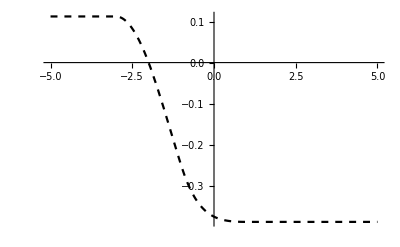

```mathematica
Plot[{NIntTRFermi[ϵ,-2,1,0,{-2,2},300]},{ϵ,-5,5},PlotStyle->{Black,{Black,Dashed}}]
```

### Now the integral with the UnitStep function

```mathematica
IntTRStepW[ϵ_,Γ_,δ_,ϵc_,{ϵmin_,ϵmax_}]:=Module[{Γδ,ϵδ,B1,B2},
Γδ=Γ+δ;
ϵδ=ϵ+δ;
B1=Piecewise[{
{CDF[TriangularDistribution[{ϵmin,ϵmax},ϵc],0],Γδ>0},
{CDF[TriangularDistribution[{ϵmin,ϵmax},ϵc],Γδ],Γδ≤0}
}];
B2=Piecewise[{
{CDF[TriangularDistribution[{ϵmin,ϵmax},ϵc],0],ϵδ>0},
{CDF[TriangularDistribution[{ϵmin,ϵmax},ϵc],ϵδ],ϵδ≤0}
}];
B1-B2
];
```

```mathematica
NIntTRStep[ϵ_,Γ_,δ_,ϵc_,{ϵmin_,ϵmax_}]:=NIntegrate[ρTR[y,ϵc,{ϵmin,ϵmax}]UnitStep[-y],{y,ϵ+δ,Γ+δ},MinRecursion->7];
```

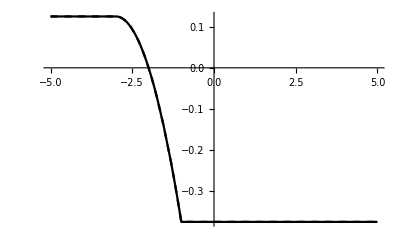

```mathematica
Plot[{NIntTRStep[ϵ,-2,1,0,{-2,2}],IntTRStepW[ϵ,-2,1,0,{-2,2}]},{ϵ,-5,5},PlotStyle->{Black,{Black,Dashed}}]
```

## Gaussian density of states (Normal distribution)

```mathematica
ρG[x_,ϵc_,σ_]:=1/(√(2 π) σ)Exp[-(x-ϵc)^2/(2 σ^2)];
CDFρG[x_,ϵc_,σ_]:=1/2 Erfc[(-x+ϵc)/(√2 σ)];
```

```mathematica
Manipulate[
Plot[ρG[x,ϵc,σ],{x,-2,2},
PlotRange->{-0.1,1},
Axes->False,Frame->True,
FrameLabel->{"ϵ-ϵ_F","DOS"},
GridLines->{None,{0}}],
{{ϵc,0,"ϵ_c"},-2,2},
{{σ,1},0.5,2},
FrameLabel->{None,None,"Gaussian Band"}
]
```

### Now the integral with the Fermi distribution function

```mathematica
NIntGFermi[ϵ_,Γ_,δ_,ϵc_,σ_,T_]:=NIntegrate[ρG[y,ϵc,σ]/(1+Exp[y/(kb T au2kcal)]),{y,ϵ+δ,Γ+δ},MinRecursion->7,MaxRecursion->20,WorkingPrecision->9];
```

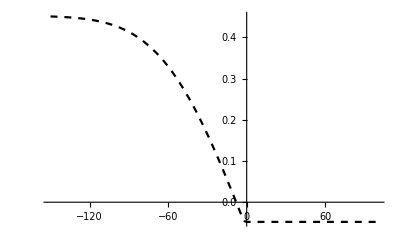

```mathematica
Plot[{NIntGFermi[ϵ,-8,2,0,50,300]},{ϵ,-150,100},PlotStyle->{Black,Dashed}]
```

### Now the integral with the UnitStep function

```mathematica
IntGStepW[ϵ_,Γ_,δ_,ϵc_,σ_]:=Module[{Γδ,ϵδ,B1,B2},
Γδ=Γ+δ;
ϵδ=ϵ+δ;
B1=Piecewise[{
{CDFρG[0,ϵc,σ],Γδ>0},
{CDFρG[Γδ,ϵc,σ],Γδ≤0}
}];
B2=Piecewise[{
{CDFρG[0,ϵc,σ],ϵδ>0},
{CDFρG[ϵδ,ϵc,σ],ϵδ≤0}
}];
B1-B2
];
```

```mathematica
NIntGStep[ϵ_,Γ_,δ_,ϵc_,σ_]:=NIntegrate[ρG[y,ϵc,σ]UnitStep[-y],{y,ϵ+δ,Γ+δ},MinRecursion->7];
```

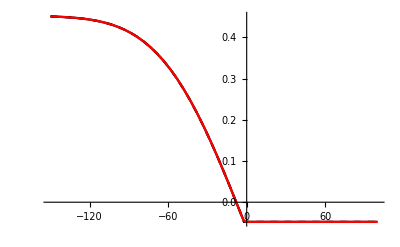

```mathematica
Plot[{NIntGStep[ϵ,-8,2,0,50],IntGStepW[ϵ,-8,2,0,50],NIntGFermi[ϵ,-8,2,0,50,300]},{ϵ,-150,100},PlotStyle->{Black,{Black,Dashed},Red}]
```

### For spectral decomposition: DOS = linear combination of Gaussians

```mathematica
totalDOSdata=Import["data/dos/pt111_dos.csv","CSV"];
pDOSdata=Import["data/dos/pt111_dos_spd_states.csv","CSV"];
totalDOS=pDOSdata⟦All,{1,2}⟧;
sDOS=pDOSdata⟦All,{1,4}⟧;
pDOS=pDOSdata⟦All,{1,6}⟧;
dDOS=pDOSdata⟦All,{1,8}⟧;
```

```mathematica
totalDOSfitykPeaks=Drop[Drop[Import["data/dos/pt111_dos_model_36G_parameters.peaks"],-1],1]⟦All,{2,3,5}⟧;
```

```mathematica
totalDOSfitykParameters=MapAt[#/(2 √(2Log[2]))&,totalDOSfitykPeaks,{All,3}];
```

```mathematica
totalDOSfitParameters=Map[{#⟦1⟧,√(2π)#⟦3⟧#⟦2⟧,#⟦3⟧}&,totalDOSfitykParameters];
```

```mathematica
totalDOSfitykF[x_]:=Module[{nG,ci,xi,σi},
nG=Length[totalDOSfitParameters];
ci=totalDOSfitParameters⟦All,2⟧;
xi=totalDOSfitParameters⟦All,1⟧;
σi=totalDOSfitParameters⟦All,3⟧;
Chop@Sum[ci⟦k⟧/(√(2π)σi⟦k⟧)Exp[-(x-xi⟦k⟧)^2/(2 σi⟦k⟧^2)],{k,1,nG}]
];
```

```mathematica
Length[totalDOSfitParameters]
```

36

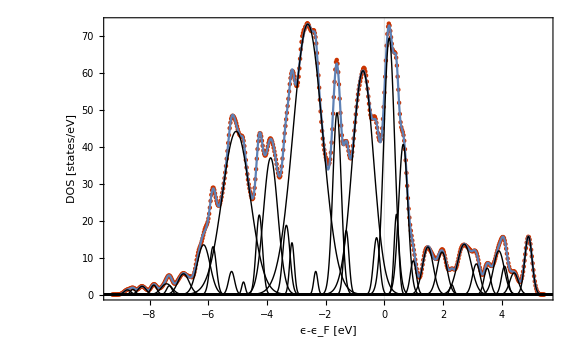

```mathematica
Show[
ListPlot[{totalDOS},
Filling->{1->None,2->Axis},
PlotTheme->{"Detailed","LargeLabels","VibrantColor"},
ImageSize->Large,
Axes->False,Frame->True,
FrameStyle->Directive[Black,Thickness[0.0025]],
GridLines->{{0},None},
GridLinesStyle->{{Black,Dashed,Thickness[0.0025]},{Black,Dotted}},
FrameLabel->{"ϵ-ϵ_F [eV]","DOS [states/eV]"}
],
Plot[totalDOSfitykF[x],{x,-10,6}],
Plot[Table[totalDOSfitParameters⟦iG,2⟧/(√(2π)totalDOSfitParameters⟦iG,3⟧)Exp[-(x-totalDOSfitParameters⟦iG,1⟧)^2/(2 totalDOSfitParameters⟦iG,3⟧^2)],{iG,1,Length[totalDOSfitParameters]}],{x,-10,6},PlotStyle->{Black,Thin},PlotRange->All]
]
```

```mathematica
IntGStepWfit[ϵ_,Γ_,δ_,totalDOSfitParameters_]:=Module[{Γδ,ϵδ,B1,B2,total,nG,ϵc,σ,ci},
Γδ=Γ+δ;
ϵδ=ϵ+δ;
total=0;
nG=Length[totalDOSfitParameters];
Do[
ϵc=totalDOSfitParameters⟦iG,1⟧;
σ=totalDOSfitParameters⟦iG,3⟧;
ci=totalDOSfitParameters⟦iG,2⟧;
B1=Piecewise[{
{CDFρG[0,ϵc,σ],Γδ>0},
{CDFρG[Γδ,ϵc,σ],Γδ≤0}
}];
B2=Piecewise[{
{CDFρG[0,ϵc,σ],ϵδ>0},
{CDFρG[ϵδ,ϵc,σ],ϵδ≤0}
}];
total+=ci(B1-B2),
{iG,1,nG}
];
total
];
```

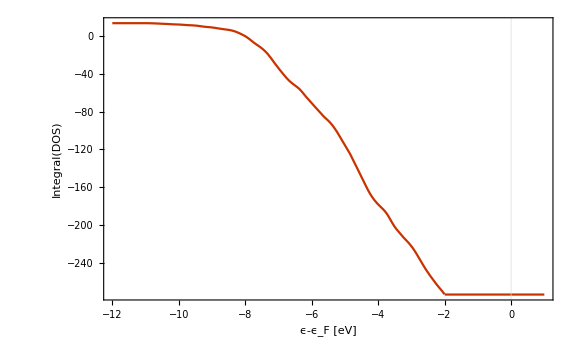

```mathematica
Plot[{IntGStepWfit[ϵ,-8,2,totalDOSfitParameters]},{ϵ,-12,1},
PlotTheme->{"Detailed","LargeLabels","VibrantColor"},
PlotLegends->None,
ImageSize->Large,
Axes->False,Frame->True,
FrameStyle->Directive[Black,Thickness[0.0025]],
GridLines->{{0},None},
GridLinesStyle->{{Black,Dashed,Thickness[0.0025]},{Black,Dotted}},
FrameLabel->{"ϵ-ϵ_F [eV]","Integral(DOS)"}
]
```

```mathematica
IntGStepWfit[0,-8,2,totalDOSfitParameters]
```

## Lorentsian density of states (Cauchy distribution) [careful, all moments are undefined!]

```mathematica
ρL[x_,ϵc_,γ_]:=1/π γ/((x-ϵc)^2+γ^2);
CDFρL[x_,ϵc_,σ_]:=1/π ArcTan[(x-ϵc)/γ]+1/2;
```

```mathematica
Manipulate[
Plot[ρL[x,ϵc,γ],{x,-2,2},
PlotRange->{-0.1,1.5},
Axes->False,Frame->True,
FrameLabel->{"ϵ-ϵ_F","DOS"},
GridLines->{None,{0}}],
{{ϵc,0,"ϵ_c"},-2,2},
{{γ,0.25},0.1,2},
FrameLabel->{None,None,"Lorentsian Band"}
]
```

### Now the integral with the Fermi distribution function

```mathematica
NIntLFermi[ϵ_,Γ_,δ_,ϵc_,γ_,T_]:=NIntegrate[ρL[y,ϵc,γ]/(1+Exp[y/(kb T au2kcal)]),{y,ϵ+δ,Γ+δ},MinRecursion->7,MaxRecursion->20,WorkingPrecision->9];
```

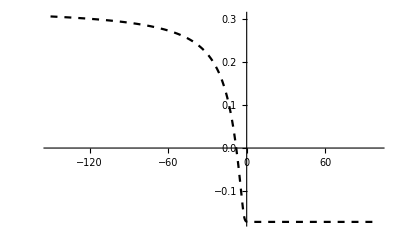

```mathematica
Plot[{NIntLFermi[ϵ,-8,2,0,10,300]},{ϵ,-150,100},PlotStyle->{Black,Dashed}]
```

### Now the integral with the UnitStep function

```mathematica
IntLStepW[ϵ_,Γ_,δ_,ϵc_,γ_]:=Module[{Γδ,ϵδ,B1,B2},
Γδ=Γ+δ;
ϵδ=ϵ+δ;
B1=Piecewise[{
{CDFρL[0,ϵc,γ],Γδ>0},
{CDFρL[Γδ,ϵc,γ],Γδ≤0}
}];
B2=Piecewise[{
{CDFρL[0,ϵc,γ],ϵδ>0},
{CDFρL[ϵδ,ϵc,γ],ϵδ≤0}
}];
B1-B2
];
```

```mathematica
NIntLStep[ϵ_,Γ_,δ_,ϵc_,γ_]:=NIntegrate[ρL[y,ϵc,γ]UnitStep[-y],{y,ϵ+δ,Γ+δ},MinRecursion->7];
```

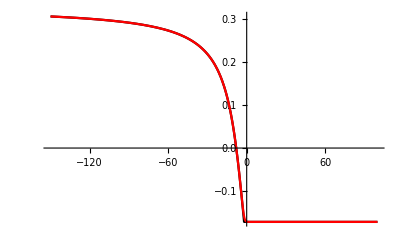

```mathematica
Plot[{NIntLStep[ϵ,-8,2,0,10],IntLStepW[ϵ,-8,2,0,10],NIntLFermi[ϵ,-8,2,0,10,300]},{ϵ,-150,100},PlotStyle->{Black,{Black,Dashed},Red}]
```